Digital Design

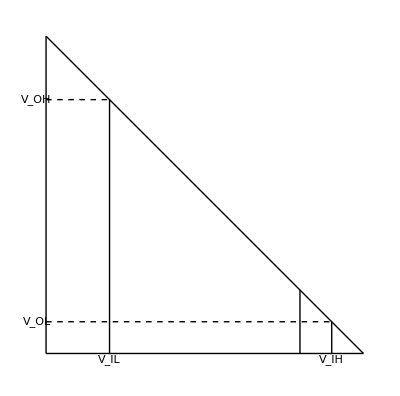

```mathematica
Graphics[{
Line[{{0,5},{5,0}}],
Line[{{1,0},{1,4}}],
Line[{{4,0},{4,1}}],
Line[{{4.5,0},{4.5,0.5}}],
{Dashing[0.01],Line[{{0,4},{1,4}}]},
{Dashing[0.01],Line[{{0,0.5},{4.5,0.5}}]},
Line[{{0,0},{5,0}}],
Line[{{0,0},{0,5}}],
Text[Subscript[V, IL],{1,-0.1}],
Text[Subscript[V, OH],{-0.15,4}],
Text[Subscript[V, IH],{4.5,-0.1}],
Text[Subscript[V, OL],{-0.15,0.5}]
}]
```

```mathematica
Subscript[V, IL]=3;Subscript[V, OH]=4;Subscript[V, IH]=3;Subscript[V, OL]=1.5;
```

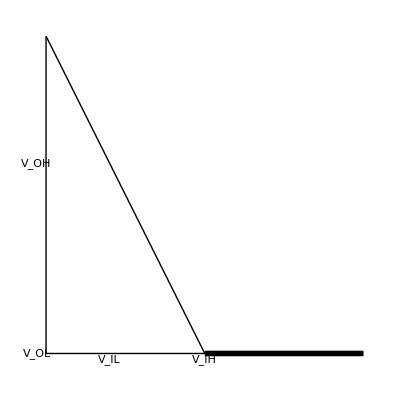

```mathematica
Graphics[{
Line[{{0,0},{5,0}}],
Line[{{0,0},{0,5}}],
Line[{{0,5},{2.5,0}}],
{Thickness[0.01],Line[{{2.5,0},{5,0}}]},
Text[Subscript[V, IL],{1,-0.1}],
Text[Subscript[V, OH],{-0.15,3}],
Text[Subscript[V, IH],{2.5,-0.1}],
Text[Subscript[V, OL],{-0.15,0}]
}]
```

Digital Design1.86

```mathematica
1,0,0->1
```

1.87

```mathematica
0,1->1
1,0->1
0,0->0
1,1->0
XOR
```

1.88

```mathematica
¬((A∩B)∪C)
```

2.13

```mathematica
AC+A^- B^-C=A B C+A B^- C+A B^- C+A^- B^-C=A C+B^-C
```

2.14

```mathematica
A^-+ B^-+C^-+A B^- =A^-+ B^-+C^-
```

```mathematica
A B C D^-+A(B^-+C^-+D^-)+A^- B^- C^-D^-=A(B^-+C^-+D^-)+A^- B^- C^-D^-=A(B^-+C^-+D^-)+B^- C^-D^-
```

2.17

```mathematica
B C+A^-B^- C^-+B C^-=B+A^-B^- C^-=B+A^-C^-
```

```mathematica
A^-(A+B^-)(A+B)+A^- B=A^-B^-(A+B)+A^- B=A^- B
```

2.20

```mathematica
1->buffer->1
```

2.36

```mathematica
Subscript[Y, 0]=Subscript[A, 6] Subscript[A, 7]^-+Subscript[A, 4] Subscript[A, 5]^-Subscript[A, 7]^-+Subscript[A, 2] Subscript[A, 3]^-Subscript[A, 5]^-Subscript[A, 7]^-+Subscript[A, 0] Subscript[A, 1]^-Subscript[A, 3]^-Subscript[A, 5]^-Subscript[A, 7]^-
```

2.40

```mathematica
C^- D^- A^- B+C^- D^- A B^-+A^- B^-
```

2.45

```mathematica
NOT 3-input NOR
```

Question 2.1

```mathematica
A B^-+A^- B
NAND==NOT OR
```

```mathematica
(1,A)NAND
```

Computer Organization

```mathematica
r={417,83,66,39449,772};m={244,70,153,35527,368};
z={134,70,135,66000,369};
{1/5∑_(i=1)^5 r[[i]]/m[[i]],1/5∑_(i=1)^5 r[[i]]/z[[i]]}//N
{1/5∑_(i=1)^5 m[[i]]/r[[i]],1/5∑_(i=1)^5 m[[i]]/z[[i]]}//N
{(∏_(i=1)^5 r[[i]]/m[[i]])^(1/5),(∏_(i=1)^5 r[[i]]/z[[i]])^(1/5)}//N
{(∏_(i=1)^5 m[[i]]/r[[i]])^(1/5),(∏_(i=1)^5 m[[i]]/z[[i]])^(1/5)}//N
```

{1.30686,1.49528}

{1.02479,1.09796}

{1.15283,1.17669}

{0.867431,1.02069}

```mathematica
r={100,1};m={1,10};
```

4-21

```mathematica
(50+5*60/4+2.5+2.5)0.05+2.5*0.95
```

8.875

```mathematica
(50+5*124/4+2.5+2.5)0.03+2.5*0.97
```

8.725

4-23

Computer Network

1-p25

```mathematica
m/(R*Subscript[D, prop])=s/R
```

1-P31

```mathematica
2 F/R;(N+1)(F/N)/R
```

1-P33

```mathematica
(N+1)(F/N+80)/R;
Solve[D[(N+1)(F/N+80)/R,N]==0,N]
```

{{N→-(√F)/(4 √5)},{N→(√F)/(4 √5)}}

```mathematica
D[(N+1)(F/N+80)/R,N]/.{N->(√F)/(4 √5)}//Simplify
D[(N+1)(F/N+80)/R,{N,2}]/.{N->(√F)/(4 √5)}//Simplify
```

0

(640 √5)/(√F R)

```mathematica
(F/S+1)(S+80)/R;
Solve[D[(F/S+1)(S+80)/R,S]==0,S]
```

{{S→-4 √5 √F},{S→4 √5 √F}}